```mathematica
{Range[Length[w]],
Table[With[{i=i},InputField[Dynamic[w[[i]]],Number,FieldSize->{7,1}]],{i,1,Length[w]}],
Table[With[{i=i},Dynamic[ScientificForm@SetPrecision[lossfuncsval[[i]],3]]],{i,1,Length[w]}],
Table[With[{i=i},Dynamic[lossfuncsval[[i]]w[[i]]]],{i,1,Length[w]}],
lossfuncsexp}ᵀ//TableForm[#,TableHeadings->{None,{"i","w","val","w.v","exp"}}]&
Dynamic[BarChart[w lossfuncsval//Reverse,BarOrigin->Left,ChartLabels->Reverse@lossfuncsexp,PlotRange->{{-0.51,2},All},AspectRatio->0.3,ImageSize->Full]]
Dynamic[Show[
ListPlot[{δ,(MAPKpp[1]-MAPKpp[0])/(dX*maxdose)}/.dat,PlotRange->3*10^0{-1,1},AxesLabel->{"Dose","MI"},PlotLegends->LineLegend[{"Native","Over Expressed"}]],
Plot[{equNative,equOE},{x,0,1}],ImageSize->Full
]]
```

i | w | val | w.v | exp
1 |  |  |  | (StotOE/StotNative-9)^2/.{p2→56.7018,p3a→0.779985,p3b→0.0987481,p3c→5.28878,p3d→0.0000190483,p4→0.339158,p5→2.29994,StotNative→3.20028,StotOE→8000.19,maxdose→0.00300001,dX→0.000104967}
2 |  |  |  | Mean[1/2 (MAPKpp[0]+MAPKpp[1])/.Last[dat]]
3 |  |  |  | MIerrorNative
4 |  |  |  | MIerrorOE
5 |  |  |  | equNative/.a_+b_ x→(a-2)^2
6 |  |  |  | equNative/.a_+b_ x→b^2
7 |  |  |  | (x-0.8)^2/.Solve[equNative==equOE]⟦1⟧
8 |  |  |  | (x-0.2)^2/.Solve[equOE==0]⟦1⟧

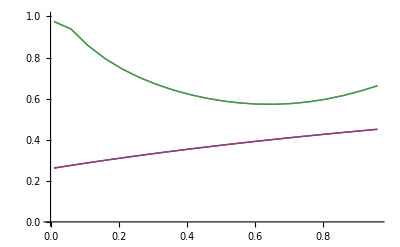

```mathematica
ListLinePlot[Flatten[Transpose[{{δ,MAPKpp[0]/MAXMAPKPP},{δ,MAPKpp[1]/MAXMAPKPP}}/.#]&/@dat,1],PlotRange->{0,1}]
```

```mathematica
TableForm[Table[With[{i=i},{
InputField[Dynamic[θ0[[i]]],Number,FieldSize->{11,1}],
InputField[Dynamic[σ0[[i]]],Number,FieldSize->{11,1}],
Dynamic[grad[[i]]]
}],{i,1,Length[θ0]}],TableHeadings->{v,{"θ0","σ0","grad"}}]
```

| θ0 | σ0 | grad
p2 |  |  | 
p3a |  |  | 
p3b |  |  | 
p3c |  |  | 
p3d |  |  | 
p4 |  |  | 
p5 |  |  | 
StotNative |  |  | 
StotOE |  |  | 
maxdose |  |  | 
dX |  |  |

```mathematica
Row[{Button["Update Lold",(SPSA`Private`Lold=Loss[SPSA`Private`θk]], ,Dynamic[SPSA`Private`Lold]}]
Dynamic[SPSA`Private`θk]
```

Update Lold

```mathematica
SPSA
grad=FDGradientP[Loss,θ0,δp];
σ0=δL/Abs@grad;
SPSA`Private`Lold=Loss[SPSA`Private`θk];
```

```mathematica
Loss[θ0]
```

97.6081

```mathematica
dX=0.0005
```

0.0005

```mathematica
sol[[-1]]
```

{5.721,{39.9352,0.644073,0.0388778,6.48011,0.0000248789,0.115405,2.90431,3.822,8752.22,0.00125665,0.0000642995}}

```mathematica
θ0
```

```mathematica
θ0={39.935231497016815,0.6440733655347445,0.03887780263284455,6.480113948617697,0.000024878875411436162,0.11540533470205612,2.9043056225369415,3.8220042675376393,8752.224246002497,0.0012566523292079355,0.00006429946675391224}
```

{39.9352,0.644073,0.0388778,6.48011,0.0000248789,0.115405,2.90431,3.822,8752.22,0.00125665,0.0000642995}

```mathematica
StotOE/StotNative/.pθ
```

2289.96

```mathematica
θ0=SetPrecision[θ0,2]
```

{40.,0.64,0.039,6.5,0.000025,0.12,2.9,3.8,8800.,0.0013,0.000064}

```mathematica
Loss[θ_?(VectorQ[#,NumericQ]&)]:=With[{pθ=Thread[v->Abs@θ]},
dat=Transpose@ParallelTable[

runsim[plist]
,{l,lenX},{s,slevel/.pθ},];


]
```

```mathematica
Flatten[{s,Log[10,slevel],.1}]/.pθ
```

{s,0.582291,3.94212,0.1}

```mathematica
slevel/.pθ
```

{3.822,8752.22}

```mathematica
1/9.
```

0.111111